```mathematica
m := 30
Γ := .005
k := (2 Sqrt[2] m Γ γ/(Pi Sqrt[m^2 + γ]))
γ  := Sqrt[m^2(m^2 + Γ^2)]
σ[e_] := (k/(e^2 -m^2)^2 + m^2 Γ^2)
```

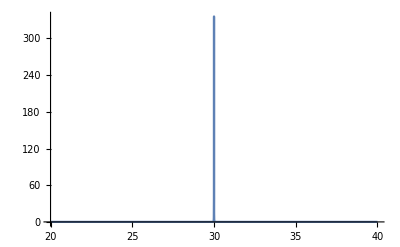

```mathematica
Plot[σ[e],{e,20,40},PlotRange->All]
```

```mathematica
σ[4]//N
```

2.25×10^6